```mathematica
A = Import["C:\Users\david\Documents\GitHub\Chart_Comparisons\Seeded_Values_for_Comparison_Project.csv", {"Data", All, 2;;3}]
```

{{37,25},{7,88},{26,65},{27,5},{91,28},{77,51},{58,29},{87,83},{58,10},{13,98},{62,52},{91,26},{18,68},{18,64},{23,3},{61,6},{90,39},{26,53},{2,96},{54,15},{27,40},{30,24},{52,65},{39,27},{3,84},{37,13},{32,83},{43,43},{28,14},{6,65},{50,76},{50,95},{71,15},{45,100},{37,5},{19,62},{84,92},{61,58},{46,10},{51,32},{39,9},{95,83},{16,41},{27,99},{28,46},{89,32},{54,19},{98,1},{98,13},{61,39}}

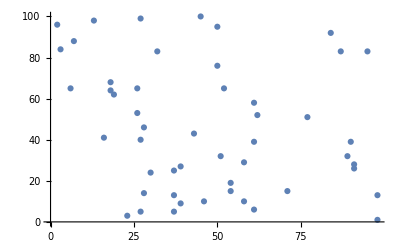

```mathematica
ListPlot[A]
```

```mathematica
B = Import["C:\Users\david\Documents\GitHub\Chart_Comparisons\Seeded_Values_for_Comparison_Project.csv", {"Data", All, 1}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
ListPlot[B,A]
```

ListPlot::nonopt: Options expected (instead of {{37,25},{7,88},{26,65},{27,5},{91,28},{77,51},{58,29},{87,83},{58,10},{13,98},{62,52},{91,26},{18,68},{18,64},{23,3},{61,6},{90,39},{26,53},{2,96},{54,15},{27,40},{30,24},«7»,{6,65},{50,76},{50,95},{71,15},{45,100},{37,5},{19,62},{84,92},{61,58},{46,10},{51,32},{39,9},{95,83},{16,41},{27,99},{28,46},{89,32},{54,19},{98,1},{98,13},{61,39}}) beyond position 1 in ListPlot[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50},{{37,25},{7,88},{26,65},{27,5},{91,28},{77,51},{58,29},{87,83},{58,10},{13,98},{62,52},«28»,{51,32},{39,9},{95,83},{16,41},{27,99},{28,46},{89,32},{54,19},{98,1},{98,13},{61,39}}]. An option must be a rule or a list of rules.

ListPlot[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50},{{37,25},{7,88},{26,65},{27,5},{91,28},{77,51},{58,29},{87,83},{58,10},{13,98},{62,52},{91,26},{18,68},{18,64},{23,3},{61,6},{90,39},{26,53},{2,96},{54,15},{27,40},{30,24},{52,65},{39,27},{3,84},{37,13},{32,83},{43,43},{28,14},{6,65},{50,76},{50,95},{71,15},{45,100},{37,5},{19,62},{84,92},{61,58},{46,10},{51,32},{39,9},{95,83},{16,41},{27,99},{28,46},{89,32},{54,19},{98,1},{98,13},{61,39}}]

```mathematica
Clist= Import["C:\Users\david\Documents\GitHub\Chart_Comparisons\Seeded_Values_for_Comparison_Project.csv"]
```

{{1,37,25},{2,7,88},{3,26,65},{4,27,5},{5,91,28},{6,77,51},{7,58,29},{8,87,83},{9,58,10},{10,13,98},{11,62,52},{12,91,26},{13,18,68},{14,18,64},{15,23,3},{16,61,6},{17,90,39},{18,26,53},{19,2,96},{20,54,15},{21,27,40},{22,30,24},{23,52,65},{24,39,27},{25,3,84},{26,37,13},{27,32,83},{28,43,43},{29,28,14},{30,6,65},{31,50,76},{32,50,95},{33,71,15},{34,45,100},{35,37,5},{36,19,62},{37,84,92},{38,61,58},{39,46,10},{40,51,32},{41,39,9},{42,95,83},{43,16,41},{44,27,99},{45,28,46},{46,89,32},{47,54,19},{48,98,1},{49,98,13},{50,61,39}}

```mathematica
Dlist = TableForm[Clist]
```

1 | 37 | 25
2 | 7 | 88
3 | 26 | 65
4 | 27 | 5
5 | 91 | 28
6 | 77 | 51
7 | 58 | 29
8 | 87 | 83
9 | 58 | 10
10 | 13 | 98
11 | 62 | 52
12 | 91 | 26
13 | 18 | 68
14 | 18 | 64
15 | 23 | 3
16 | 61 | 6
17 | 90 | 39
18 | 26 | 53
19 | 2 | 96
20 | 54 | 15
21 | 27 | 40
22 | 30 | 24
23 | 52 | 65
24 | 39 | 27
25 | 3 | 84
26 | 37 | 13
27 | 32 | 83
28 | 43 | 43
29 | 28 | 14
30 | 6 | 65
31 | 50 | 76
32 | 50 | 95
33 | 71 | 15
34 | 45 | 100
35 | 37 | 5
36 | 19 | 62
37 | 84 | 92
38 | 61 | 58
39 | 46 | 10
40 | 51 | 32
41 | 39 | 9
42 | 95 | 83
43 | 16 | 41
44 | 27 | 99
45 | 28 | 46
46 | 89 | 32
47 | 54 | 19
48 | 98 | 1
49 | 98 | 13
50 | 61 | 39

```mathematica
ListPointPlot3D[%36]
```

-Graphics3D-